```mathematica
SetDirectory[NotebookDirectory[]];
edgesList=Import["allEdges.csv"];
```

```mathematica
edges=#⟦1⟧<->#⟦2⟧&/@edgesList[[All,{1,2}]];
```

```mathematica
Length[student]
Length[edges]
```

0

13536

```mathematica
SetSystemOptions["GraphOptions"->{"EdgeCountThreshold"->50000,"VertexCountThreshold"->50000}];
```

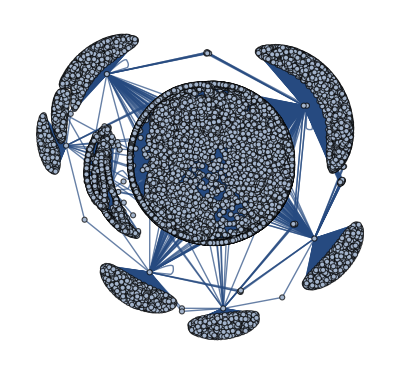

```mathematica
T=Graph[edges]
```